Задание 2.1.29
-Graphics-
-Graphics-

Определим метод бисекции

```mathematica
BisecMethod[f_,A_,B_,epselon_]:=(b=B;a=A;
While[(b-a)>=2epselon,y=(a+b)/2;
If[f[y]f[a]<0,b=y,If[f[y]f[b]<0,a=y]]
];
Return[y//N]);
```

Данные задачи

```mathematica
ϵ=10^-10;a0=0;b0=3;
f[x_]:=x^4-26/5 x^2+1;
g[x_]:=x^4-10 x^2+25;
```

Найдем аналитически корни уравнения f[x] = 0;

Пусть t = x^2
t^2-26/5 t+1=0
D = (-26/5)^2-4 = 576/25
t_(1,2) = (26/5 +
_ √(576/25))/2 ; t_1= 5, t_2 = 1/5
Вернемся к переменной x
x_1 = √5, x_2= -√5, x_3=1/(√5),x_4 = 1/(-√5)

Сделаем проверку встроеными методами пакета

```mathematica
roots = Solve[{f[x]==0},x]
```

{{x→-1/(√5)},{x→1/(√5)},{x→-√5},{x→√5}}

Локализуем корни графически

Для этого сначала построим график функции f[x] на промежутке [a0; b0], а затем локализуем каждый корень, который попадет в рассматриваемый промежуток

График функции:

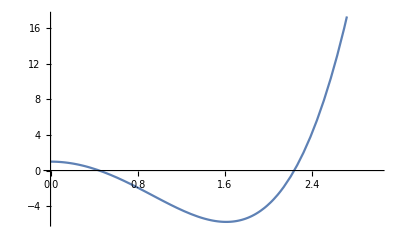

Локализуем два корня, входящие в промежуток:

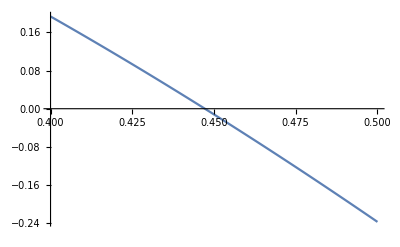

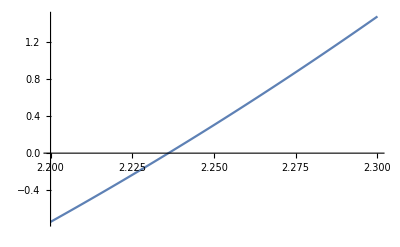

```mathematica
"График функции:"
Plot[f[x],{x,a0,b0}]
"Локализуем два корня, входящие в промежуток:"
Plot[f[x],{x,0.4,0.5}]
Plot[f[x],{x,2.2,2.3}]
```

Найдем корни с помощью функции BisecMethod

```mathematica
BisecMethod[f,0.4,0.5,ϵ]
BisecMethod[f,2.2,2.3,ϵ]
```

0.447214

2.23607

Сравним с ранее полученными корнями

```mathematica
N@roots
```

{{x→-0.447214},{x→0.447214},{x→-2.23607},{x→2.23607}}

Для функции g[x]

Пусть t = x^2
t^2-10 t+25=0
D = 100-100=0
t_(1,2)= 10/2=5
Вернемся к переменной x
x_(1,2) = -√5, x_(3,4)= √5

Проверка

```mathematica
Solve[{g[x]==0},x]
```

{{x→-√5},{x→-√5},{x→√5},{x→√5}}

График функции:

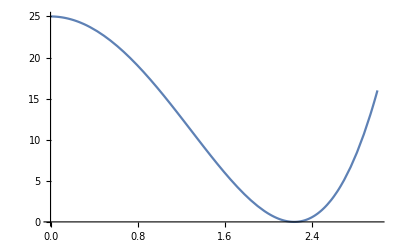

```mathematica
"График функции:"
Plot[g[x],{x,a0,b0}]
```

Получили, что в промежутке [a0; b0] лежит корень двойной кратности, следовательно мы не можем пременить метод бисекции для нахождения этого корня